```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
PartLoopByGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使った部分巡回路の構築 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
EdgeSolution=AppendEdgeProcess
]
]
];
EdgeSolution=EdgeRules[FindCycle[UndirectedGraph[EdgeSolution]][[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
DelEle[list_,element_]:=Delete[list,FirstPosition[list,element]](* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=Delete[list,Table[FirstPosition[list,i],{i,elementlist}]](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair ２つの枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアーとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
PartLoopByNewUndirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮しない、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
UndirectedGraph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
PartLoopByNewDirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮する、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
Graph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
RestEdgeSort[Edge_,Cost_]:=
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]][[
Ordering[Cost[[
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]
]]]]
]](* 残りの枝でのソート(与えられた枝をRulegから引いたエッジリストの中でのソート) *)
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)
```

### 渦電流の計算

```mathematica
Pin={{1.7,2.13},{0.67,1.08},{2.37,0.24},{5.3,3.45},{0.45,0.73},{0.76,1.47},{2.78,3.2},{4.14,2.26},{2.42,2.78},{5.24,2.42}}(*Point input*)
```

{{1.7,2.13},{0.67,1.08},{2.37,0.24},{5.3,3.45},{0.45,0.73},{0.76,1.47},{2.78,3.2},{4.14,2.26},{2.42,2.78},{5.24,2.42}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

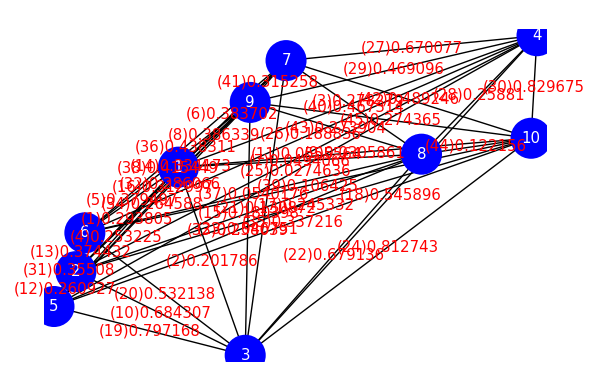

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

### TSPの解

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

1→2 | 1→3 | 1→4 | 1→5 | 1→6 | 1→7 | 1→8 | 1→9 | 1→10 | 2→3
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

2→4 | 2→5 | 2→6 | 2→7 | 2→8 | 2→9 | 2→10 | 3→4 | 3→5 | 3→6
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

3→7 | 3→8 | 3→9 | 3→10 | 4→5 | 4→6 | 4→7 | 4→8 | 4→9 | 4→10
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

5→6 | 5→7 | 5→8 | 5→9 | 5→10 | 6→7 | 6→8 | 6→9 | 6→10 | 7→8
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

7→9 | 7→10 | 8→9 | 8→10 | 9→10
41 | 42 | 43 | 44 | 45

```mathematica
Curr
```

{0.293805,0.201786,-0.278279,0.253225,0.379497,-0.383702,-0.0494066,-0.386339,-0.0305861,0.684307,-0.0555564,0.260927,-0.374432,-0.334173,0.180398,-0.312997,0.245332,0.545896,-0.797168,-0.532138,0.130872,0.679136,0.046751,0.812743,-0.0274636,0.188836,0.670077,-0.25881,0.469096,-0.829675,-0.35508,-0.286066,0.258039,-0.264588,0.337216,-0.438311,0.0540176,-0.415449,0.106425,-0.467314,0.315258,-0.489246,0.273904,0.122156,-0.274365}

```mathematica
Reverse[Ordering[Abs[Curr]]](* 降順 *)
```

{30,24,19,10,22,27,18,20,42,29,40,36,38,8,6,5,13,31,35,14,41,16,1,32,3,45,43,34,12,28,33,4,17,2,26,15,21,44,39,11,37,7,23,9,25}

```mathematica
PDSort=Ordering[PD//N](* 昇順 *)
```

{13,12,41,31,8,30,44,5,1,6,40,28,43,4,10,19,2,20,38,16,7,27,23,42,36,22,45,34,29,21,14,32,37,9,24,15,3,33,18,39,17,26,35,11,25}

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{5.00621,9.93746,13.7789,7.41172,3.02655,3.96218,49.4562,2.51075,116.126,2.77099,93.6225,1.58435,1.06895,8.95067,20.317,7.79488,19.4121,7.96149,2.48572,3.80743,22.8335,3.95467,54.3409,4.43445,202.474,26.229,3.77922,6.42108,6.30341,1.24355,2.25952,11.8699,15.4807,10.7455,15.0627,6.06777,64.2585,5.09001,43.0314,3.53775,1.75467,5.27484,6.56028,9.09964,10.3617}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{13,30,12,41,31,19,8,10,5,40,27,20,22,6,24,1,38,42,36,29,28,43,4,16,18,14,44,2,45,34,32,3,35,33,17,15,21,26,39,7,23,37,11,9,25}

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

{12.8284,{1,6,2,5,3,8,10,4,7,9,1}}

-Graphics-

### 電流コストによる新しいgreedyを用いた解法

```mathematica
Clear[CurrCost]
```

```mathematica
CurrSort=Ordering[Abs[1/Curr]//N]
```

{30,24,19,10,22,27,18,20,42,29,40,36,38,8,6,5,13,31,35,14,41,16,1,32,3,45,43,34,12,28,33,4,17,2,26,15,21,44,39,11,37,7,23,9,25}

```mathematica
PartLoopByNewUndirectedGreedyFromSort[CurrSort]
Graphics[Line[Pin[[%]]]]
```

{3,10,4,3}

-Graphics-

```mathematica
PartLoopByNewDirectedGreedyFromSort[CurrSort]
Graphics[Line[Pin[[%]]]]
```

{3,6,7,8,3}

-Graphics-

```mathematica
OutLoop1={EdgeSolution}
```

{{3→8,8→7,7→6,6→3}}

```mathematica
RestVertex[OutLoop1[[1]]]
```

{1,2,4,5,9,10}

```mathematica
Table[Min[TriTourDiffList[OutLoop1[[1]],i]],{i,{1,2,4,5,9,10}}]
```

{0.00929271,0.270377,2.54097,0.757769,0.00824448,2.02988}

```mathematica
OutLoop1=ContinuousInsertVertexLoop[OutLoop1[[1]]]
```

{{3→8,8→7,7→6,6→3},{3→8,8→7,6→3,7→9,9→6},{3→8,8→7,6→3,7→9,9→1,1→6},{3→8,8→7,7→9,9→1,1→6,6→2,2→3},{3→8,8→7,7→9,9→1,1→6,6→2,2→5,5→3}}

{1,9,7,8,3,5,2,6,1}

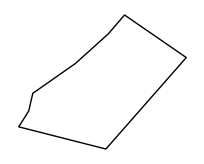

```mathematica
VertexSortFromLoopEdgeList[OutLoop1[[-1]]]
Graphics[Line[Pin[[%]]]]
```

```mathematica
RestVertex[OutLoop1[[-1]]]
```

{4,10}

```mathematica
TriTourDiffList[OutLoop1[[-1]],4]
```

{3.32223,2.54097,4.9361,5.82128,7.63879,9.75406,10.3486,7.92526}

```mathematica
TriTourDiffList[OutLoop1[[-1]],10]
```

{2.02988,2.03903,4.87041,5.42474,6.98291,8.94177,9.42839,6.70192}

```mathematica
OutLoop2=InsertVertexLoop[OutLoop1[[-1]]]
```

{8→7,7→9,9→1,1→6,6→2,2→5,5→3,3→10,10→8}

```mathematica
OutLoop3=InsertVertexLoop[OutLoop2]
```

{8→7,7→9,9→1,1→6,6→2,2→5,5→3,3→10,10→4,4→8}

```mathematica
RestVertex[OutLoop3]
```

{}

{1,9,7,8,4,10,3,5,2,6,1}

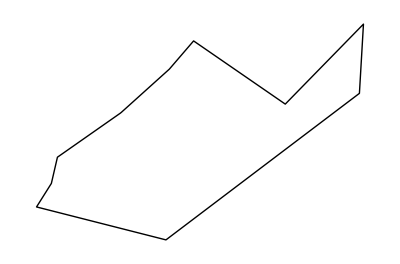

```mathematica
VertexSortFromLoopEdgeList[OutLoop3]
Graphics[Line[Pin[[%]]]]
```

### 距離と電流コストによるgreedyを用いた解法

```mathematica
PartLoopByGreedyFromSort[PDCurrCostSort]
Graphics[Line[Pin[[%]]]]
```

{2,6,5,2}

-Graphics-

```mathematica
OutLoop1=EdgeRules[EdgeSolution]
```

{2→6,6→5,5→2}

```mathematica
RestVertexList=DelEdgeVertexList[Ruleg,{2,6,5,2}]
```

{1→3,1→4,1→7,1→8,1→9,1→10,3→4,3→7,3→8,3→9,3→10,4→7,4→8,4→9,4→10,7→8,7→9,7→10,8→9,8→10,9→10}

```mathematica
EdgeNumList[RestVertexList][[Ordering[NewCost[[EdgeNumList[RestVertexList]]]]]]
```

{30,41,8,40,27,22,6,24,42,29,28,43,18,44,2,45,3,21,7,23,9}

{1,4,10,3,8,7,9,1}

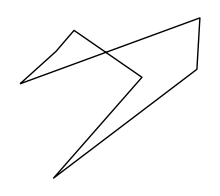

```mathematica
PartLoopByGreedyFromSort[{30,41,8,40,27,22,6,24,42,29,28,43,18,44,2,45,3,21,7,23,9}]
Graphics[Line[Pin[[%]]]]
```

```mathematica
OutLoop2=EdgeRules[EdgeSolution]
```

{4→1,1→9,9→7,7→8,8→3,3→10,10→4}

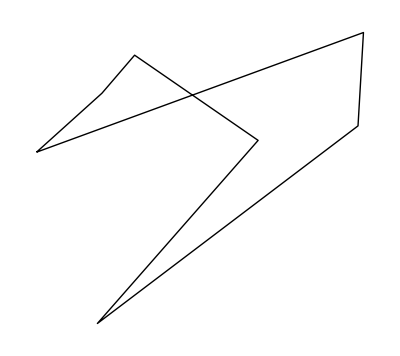
```mathematica
Show[-Graphics-,-Graphics-]
```

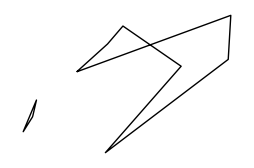

```mathematica
MinSquareTourDiffEdgePair[OutLoop1,OutLoop2]
```

{6→5,8→3}

```mathematica
DelEle[OutLoop1,OutLoop1[[2]]]
```

{2→6,5→2}

```mathematica
OutLoop2
```

{4→1,1→9,9→7,7→8,8→3,3→10,10→4}

```mathematica
OutLoop2[[5]]
```

8→3

```mathematica
MinEdgeReconstPair[OutLoop1[[{2,5}[[1]]]],OutLoop2[[{2,5}[[2]]]]][[2]]
```

{6→8,5→3}

```mathematica
Join[DelEle[OutLoop1,OutLoop1[[2]]],DelEle[OutLoop2,OutLoop2[[5]]],MinEdgeReconstPair[OutLoop1[[{2,5}[[1]]]],OutLoop2[[{2,5}[[2]]]]][[2]]]
```

{2→6,5→2,4→1,1→9,9→7,7→8,3→10,10→4,6→8,5→3}

```mathematica
JoinPartLoop[OutLoop1,OutLoop2]
```

{2→6,5→2,4→1,1→9,9→7,7→8,3→10,10→4,6→8,5→3}

{1,9,7,8,6,2,5,3,10,4,1}

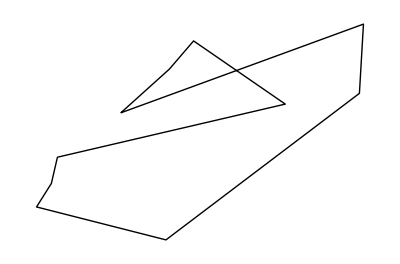

```mathematica
VertexSortFromLoopEdgeList[{2->6,5->2,4->1,1->9,9->7,7->8,3->10,10->4,6->8,5->3}]
Graphics[Line[Pin[[%]]]]
```

### 距離と電流コストによる新しいgreedyを用いた解法

```mathematica
PartLoopByNewUndirectedGreedyFromSort[PDCurrCostSort]
Graphics[Line[Pin[[%]]]]
```

{2,5,6,2}

-Graphics-

{1,9,7,8,3,6,1}

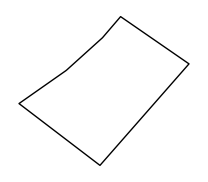

```mathematica
PartLoopByNewDirectedGreedyFromSort[PDCurrCostSort]
Graphics[Line[Pin[[%]]]]
```

```mathematica
OutLoop1={EdgeSolution}
```

{{6→3,3→8,8→7,7→9,9→1,1→6}}

```mathematica
OutLoop1=ContinuousInsertVertexLoop[OutLoop1[[1]]]
```

{{6→3,3→8,8→7,7→9,9→1,1→6},{3→8,8→7,7→9,9→1,1→6,6→2,2→3},{3→8,8→7,7→9,9→1,1→6,6→2,2→5,5→3}}

{1,9,7,8,3,5,2,6,1}

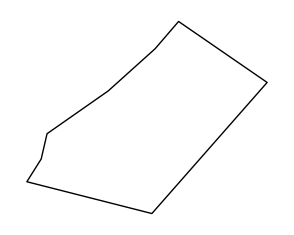

```mathematica
VertexSortFromLoopEdgeList[OutLoop1[[-1]]]
Graphics[Line[Pin[[%]]]]
```

```mathematica
RestVertex[OutLoop1[[-1]]]
```

{4,10}

```mathematica
OutEdgeList1={RestVertex[OutLoop1[[-1]]][[1]]-> RestVertex[OutLoop1[[-1]]][[2]]}
```

{4→10}

```mathematica
SquareTourDiffList[OutLoop1[[-1]],OutEdgeList1]
```

{{1.5484},{0.958961},{3.79034},{4.50702},{6.23368},{8.28339},{8.83557},{6.15144}}

```mathematica
MinSquareTourDiffEdgePair[OutLoop1[[-1]],OutEdgeList1]
```

{8→7,4→10}

```mathematica
MinEdgeReconstPair[MinSquareTourDiffEdgePair[OutLoop1[[-1]],OutEdgeList1]]
```

{3.64395,{8→10,7→4}}

```mathematica
Join[DelEleList[Join[OutLoop1[[-1]],OutEdgeList1],{MinSquareTourDiffEdgePair[OutLoop1[[-1]],OutEdgeList1][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[OutLoop1[[-1]],OutEdgeList1]][[2]]]
```

{3→8,7→9,9→1,1→6,6→2,2→5,5→3,4→10,8→10,7→4}

{1,9,7,4,10,8,3,5,2,6,1}

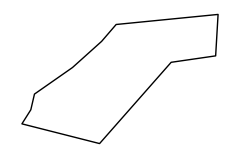

```mathematica
VertexSortFromLoopEdgeList[{3->8,7->9,9->1,1->6,6->2,2->5,5->3,4->10,8->10,7->4}]
Graphics[Line[Pin[[%]]]]
```